```mathematica
localdir = "C:\\Users\\tramiada\\OneDrive\\Projects\\gen_spe\\Figure2\\Panel def\\";
```

## Figure 2def

```mathematica
ps2  ={{Black,AbsoluteDashing[{15,5}],AbsoluteThickness[th+1]},{Gray,AbsoluteDashing[{15,5}],AbsoluteThickness[th+1]}};
```

### Figure 2d: Establishment without competition

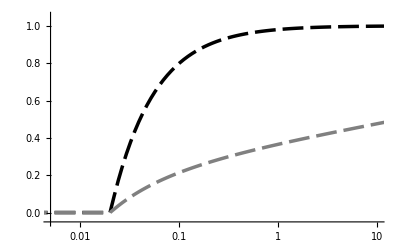

```mathematica
(*Establishment without competition*)
DATA={};plot1={};
data = Import[localdir<>"with_add_high_fig2_MF_rk4_est_True_z_1_nu_0.125_coeff_a_1_M_5_time_100000_dt_1_dq_0.01.csv"];
gdata= data[[All,{1,3}]];
sdata= data[[All,{1,4}]];

fig2d=ListLogLinearPlot[{gdata,sdata},PlotStyle->ps2,Joined->True,AxesStyle->as2,PlotRange->prange,AxesOrigin->ao,Ticks->tx]
(*est1=Show[plot1,plot2,ImageSize->Large,AxesStyle->Directive[asz,Thick]]*)
```

```mathematica
Export[localdir<>"fig2d.jpg",fig2d,ImageResolution-> 200]
```

C:\Users\tramiada\OneDrive\Projects\gen_spe\Figure2\Panel def\fig2d.jpg

### Figure 2e: Establishment with competition, no difference in a

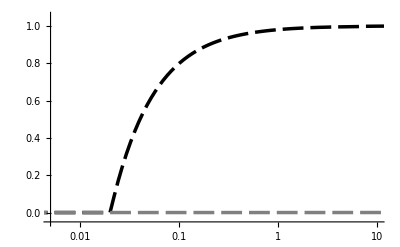

```mathematica
(*Establishment with competition*)
data= Import[localdir<>"with_add_high_fig2_MF_rk4_est_True_z_0_nu_0.125_coeff_a_1_M_5_time_100000_dt_1_dq_0.01.csv"];
gdata= data[[All,{1,3}]];
sdata= data[[All,{1,4}]];


fig2e=ListLogLinearPlot[{gdata,sdata},PlotStyle->ps2,Joined->True, AxesStyle->as2,PlotRange->prange,AxesOrigin->ao,Ticks->tx]
```

```mathematica
Export[localdir<>"fig2e.jpg",fig2e,ImageResolution-> 200]
```

C:\Users\tramiada\OneDrive\Projects\gen_spe\Figure2\Panel def\fig2e.jpg

### Figure 2f: Establishment with competition, difference in a, generalist 80% lower

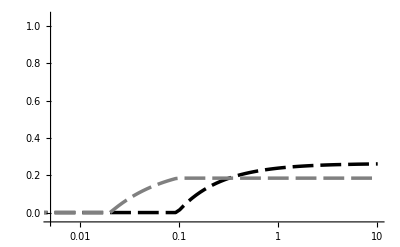

```mathematica
(*Establishment without competition*)
data= Import[localdir<>"with_add_high_fig2_MF_rk4_est_True_z_0_nu_0.125_coeff_a_0.8_M_5_time_100000_dt_1_dq_0.01.csv"];
gdata= data[[All,{1,3}]];
sdata= data[[All,{1,4}]];


fig2f=ListLogLinearPlot[{gdata,sdata},PlotStyle->ps2,Joined->True, AxesStyle->as2,PlotRange->prange,AxesOrigin->ao,Ticks->tx]
```

```mathematica
Export[localdir<>"fig2f.jpg",fig2f,ImageResolution-> 200]
```

C:\Users\tramiada\OneDrive\Projects\gen_spe\Figure2\Panel def\fig2f.jpg